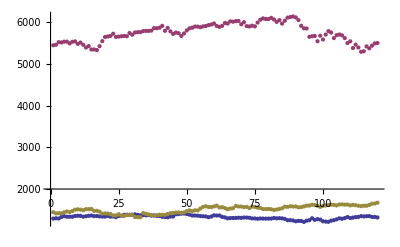

```mathematica
{hedge,dax,d2}=Transpose[Import["c:\\kurse.dat","Table"]];ListPlot[{hedge,dax,d2}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];d2=Log[d2];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];d2=Differences[d2];
```

```mathematica
w=Transpose[{hedge,dax,d2}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
d2=Transpose[w][[3]];
```

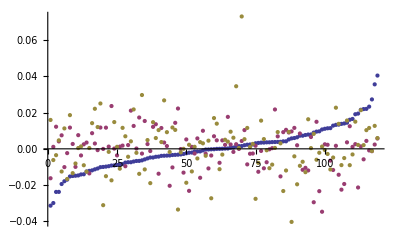

```mathematica
ListPlot[Transpose[w][[1;;3]],PlotRange->All]
```

```mathematica
min0=Min[Transpose[w][[1]]];wN=Length[hedge];nn=wN;
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<=w[[i,1]]  && #[[2]]<=w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
hedgeI=Table[{hedge[[i]],(i-1)/(nn-1)},{i,nn}];
daxI=Table[{sdax[[i]],(i-1)/(nn-1)},{i,nn}];W=F;Co=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[daxI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
ListPointPlot3D[Co]
```

-Graphics3D-

```mathematica
h=Import["C:\\delaunay.txt","Table"];c=Drop[Import["c:\\empcopula.dat","Table"],1];
g=Import["c:\\copulasample.txt","Table"];cc=Drop[Import["c:\\empcopula.dat","Table"],1];cc=Transpose[Transpose[cc][[1;;3]]];hh=Table[Subsets[h[[i]],{3}],{i,Length[h]}][[1;;Length[h]]];
Graphics3D[{{PointSize[Large],Red,Table[Point[cc[[i]]],{i,Length[cc]}]},{PointSize[Large],Blue,Point[#]&/@{cc[[1]],cc[[2]],cc[[3]],cc[[5]],cc[[4]]}},{Opacity[0.1],Table[Polygon[cc[[#+1]]&/@hh[[j]]],{j,Length[hh]}]}}]
```

-Graphics3D-

```mathematica
n=15;Export["c:\\empCopula.dat",Join[RandomInteger[n,{n,4}],{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,1,0,0},{1,0,0,0},{1,1,0,0},{1,0,1,0},{0,1,1,0}}]]
```

c:\empCopula.dat

```mathematica
i=22;ab=Inverse[{#[[1]],#[[2]],#[[3]],1}&/@(cc[[#+1]]&/@h[[i]])].(#[[4]]&/@(c[[#+1]]&/@h[[i]]));h[[i]]
ab//N
t[u_]:=ab.Append[u,1];t[cc[[#+1]]]-c[[#+1,4]]&/@h[[i]]
```

{2,4,7,14}

{0.628319,-0.557522,-0.823009,15.4159}

{0,0,0,0}

```mathematica
c[[1,4]]
```

14

```mathematica
cc[[1,3]]
```

5

```mathematica
h=.;i=.;a=.;c=.;
```

```mathematica
f[i_]:={C[[Triangs[[p,i]],e]],C[[Triangs[[p,i]],1]],C[[Triangs[[p,i]],2]],1}
```

```mathematica
h[[37]]
```

{8,11,12,13}

```mathematica
ListPointPlot3D[cc]
```

-Graphics3D-

```mathematica
CForm[Det[{f[a],f[b],f[c],{A[[e]],A[[1]],A[[2]],1}}]]
```

Part::pspec: Part specification p is neither an integer nor a list of integers.

Part::pspec: Part specification Triangs ⟦ p, a ⟧ is neither an integer nor a list of integers.

Part::pspec: Part specification p is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

Part::partd: Part specification A ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification A ⟦ 2 ⟧ is longer than depth of object.

A[e]*C[Triangs[p][a]][2]*C[Triangs[p][b]][1] - A[2]*C[Triangs[p][a]][e]*C[Triangs[p][b]][1] - 
   A[e]*C[Triangs[p][a]][1]*C[Triangs[p][b]][2] + A[1]*C[Triangs[p][a]][e]*C[Triangs[p][b]][2] + 
   A[2]*C[Triangs[p][a]][1]*C[Triangs[p][b]][e] - A[1]*C[Triangs[p][a]][2]*C[Triangs[p][b]][e] - 
   A[e]*C[Triangs[p][a]][2]*C[Triangs[p][c]][1] + A[2]*C[Triangs[p][a]][e]*C[Triangs[p][c]][1] + 
   A[e]*C[Triangs[p][b]][2]*C[Triangs[p][c]][1] - C[Triangs[p][a]][e]*C[Triangs[p][b]][2]*C[Triangs[p][c]][1] - 
   A[2]*C[Triangs[p][b]][e]*C[Triangs[p][c]][1] + C[Triangs[p][a]][2]*C[Triangs[p][b]][e]*C[Triangs[p][c]][1] + 
   A[e]*C[Triangs[p][a]][1]*C[Triangs[p][c]][2] - A[1]*C[Triangs[p][a]][e]*C[Triangs[p][c]][2] - 
   A[e]*C[Triangs[p][b]][1]*C[Triangs[p][c]][2] + C[Triangs[p][a]][e]*C[Triangs[p][b]][1]*C[Triangs[p][c]][2] + 
   A[1]*C[Triangs[p][b]][e]*C[Triangs[p][c]][2] - C[Triangs[p][a]][1]*C[Triangs[p][b]][e]*C[Triangs[p][c]][2] - 
   A[2]*C[Triangs[p][a]][1]*C[Triangs[p][c]][e] + A[1]*C[Triangs[p][a]][2]*C[Triangs[p][c]][e] + 
   A[2]*C[Triangs[p][b]][1]*C[Triangs[p][c]][e] - C[Triangs[p][a]][2]*C[Triangs[p][b]][1]*C[Triangs[p][c]][e] - 
   A[1]*C[Triangs[p][b]][2]*C[Triangs[p][c]][e] + C[Triangs[p][a]][1]*C[Triangs[p][b]][2]*C[Triangs[p][c]][e]

```mathematica
j=.
```

```mathematica
f[j]
```

Part::pspec: Part specification j is neither an integer nor a list of integers.

Part::partd: Part specification C ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification C ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification C ⟦ 3, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

Part::pspec: Part specification j is neither an integer nor a list of integers.

{C⟦j,e⟧,C⟦1,1⟧,C⟦2,2⟧,C⟦3,3⟧}